```mathematica
unitCell[x_,y_]:={Black,
,Line[{{x,y},{x,y+2/3 Sin[120 Degree]}}],Line[{{x,y},{x+Cos[30 Degree]/2,y-Sin[30 Degree]/2}}],Line[{{x,y},{x-Cos[30 Degree]/2,y-Sin[30 Degree]/2}}],Red,Disk[{x,y},0.1],Blue,Disk[{x,y+2/3 Sin[120 Degree]},0.1]}
```

```mathematica
Block[{unitVectA={Cos[120 Degree],Sin[120 Degree]},unitVectB={1,0}},Table[(*unitCell@@*)(unitVectA j+unitVectB k),{j,0,1},{k,Ceiling[j/2],10+Ceiling[j/2]}]]
```

{{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0}},{{1/2,(√3)/2},{3/2,(√3)/2},{5/2,(√3)/2},{7/2,(√3)/2},{9/2,(√3)/2},{11/2,(√3)/2},{13/2,(√3)/2},{15/2,(√3)/2},{17/2,(√3)/2},{19/2,(√3)/2},{21/2,(√3)/2}}}

```mathematica
Export["test.pdf",Graphics[Block[{unitVectA={Cos[120 Degree],Sin[120 Degree]},unitVectB={1,0}},Table[unitCell@@(unitVectA j+unitVectB k),{j,0,35},{k,Ceiling[j/2],20+Ceiling[j/2]}]]]]
```

test.pdf

```mathematica
Graphics[Block[{unitVectA={Cos[120 Degree],Sin[120 Degree]},unitVectB={1,0}},Table[unitCell@@(unitVectA j+unitVectB k),{j,0,3},{k,Ceiling[j/2],2+Ceiling[j/2]}]],ImageSize->500]
```

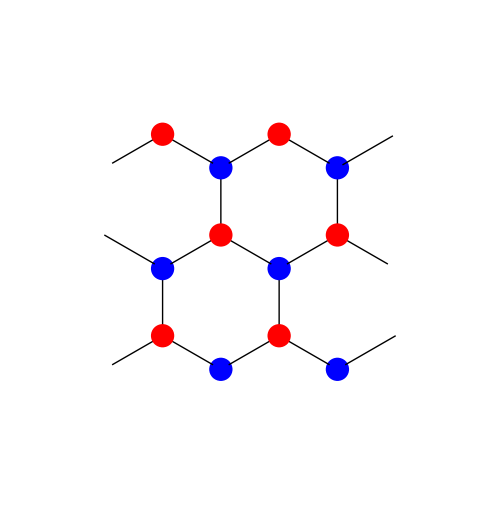

-Graphics-

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter2/6agnr.pdf",Rotate[%20,180Degree]]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter2/6agnr.pdf

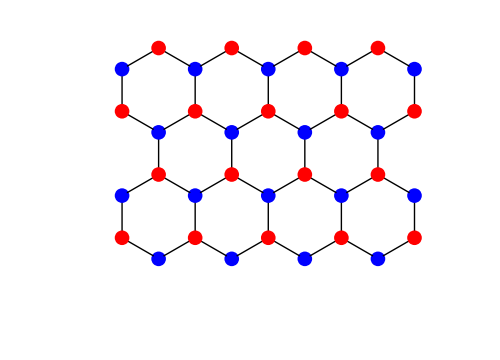

```mathematica
Rotate[%9,90Degree]
```

-Graphics-

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter2/9agnr.pdf",%11]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter2/9agnr.pdf

```mathematica
Export["~/Desktop/Thesis/thesis18jun/Images/Chapter2/graphene.pdf",Show[%9,PlotRange->{{1.5,20},{1.5,20}}]]
```

~/Desktop/Thesis/thesis18jun/Images/Chapter2/graphene.pdf

```mathematica
f[x_]:=Table[{x,(y+1)Sqrt[3]/2},{y,Range[0,5,2]}]
```

```mathematica
g[x_]:= Table[{x+1/2,Sqrt[3]*y},{y,Range[0,3,1]}]
```

```mathematica
h[x_]:=Join[f[x],g[x],g[x+0.5],f[x+1.5]]
```

```mathematica
h[0]//SortBy
```

SortBy[{{0,(√3)/2},{0,(3 √3)/2},{0,(5 √3)/2},{1/2,0},{1/2,√3},{1/2,2 √3},{1/2,3 √3},{1.,0},{1.,√3},{1.,2 √3},{1.,3 √3},{1.5,(√3)/2},{1.5,(3 √3)/2},{1.5,(5 √3)/2}}]

```mathematica
points=Module[{J=h[0]},Do[J=Join[h[x],J],{x,Range[0,30,2]}];J=J]
```

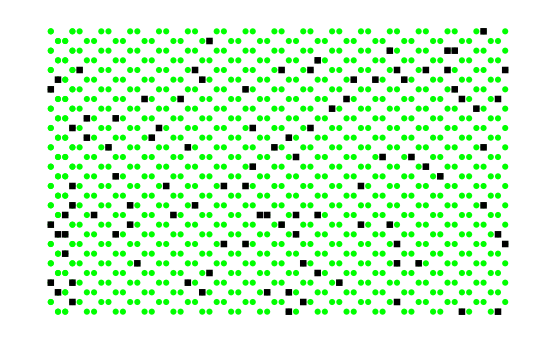

```mathematica
ListPlot[{points,RandomSample[points,100]},PlotStyle->{Green,Black},PlotMarkers->Automatic,Axes->False,ImageSize->Full]
```